# Infinite Square Well

## Constants

```mathematica
hbar=1;
```

## Energy Eigenmodes

```mathematica
k[n_,a_]:=n π/a
ω[n_,a_,m_]:=hbar k[n,a]^2/(2m)
```

```mathematica
eigen[n_,a_,m_]:=Function[{x,t},Evaluate[Sqrt[2/a]Sin[k[n,a]x]Exp[-I ω[n,a,m]t]]]
```

## Time Evolution

Define the normalized state that results from measuring s0 with FWHM Δs:

```mathematica
phi[s_,s0_,Δs_]:=2/Sqrt[3Δs]Cos[(s-s0)/Δs π/2]^2
```

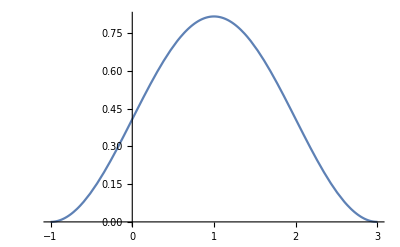

```mathematica
Plot[phi[s,1,2],{s,-1,3}]
```

Check the normalization:

```mathematica
Integrate[phi[s,s0,Δs]^2,{s,s0-Δs,s0+Δs}]
```

1

Calculate the energy eigenmode coefficients for this state. First the general case:

```mathematica
xcoef[n_,s0_,Δs_]:= Evaluate[
Sqrt[2]Integrate[Sin[n π s]phi[s,s0,Δs],{s,s0-Δs,s0+Δs},Assumptions->{Δs>0,Δs<s0<1-Δs,n∈Integers,n>0}]
]
```

Next the special case Δs = 1/n:

```mathematica
xcoef[n_,s0_]:=Evaluate[
Sqrt[2]Integrate[Sin[n π s]phi[s,s0,1/n],{s,s0-1/n,s0+1/n},Assumptions->{1/n<s0<1-1/n,n∈Integers,n>0}]
]
xcoef[n_,s0_,Δs_]:=xcoef[n,s0]/; n Δs==1
```

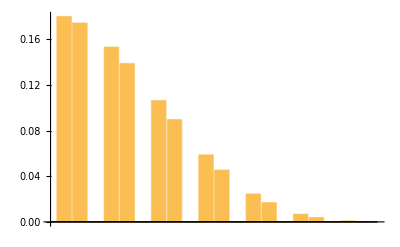

```mathematica
BarChart[Table[xcoef[n,1/3,1/11]^2,{n,1,20}]]
```

Check that coefficients are normalized correctly:

```mathematica
NSum[xcoef[n,0.45,2./11.]^2,{n,1,Infinity}]
```

0.999999

Prepare a state in an energy eigenmode:

```mathematica
emode[n_,nmax_]:=Table[KroneckerDelta[n,j],{j,nmax}]
```

Prepare a state in an approximate position eigenmode:

```mathematica
xmode[s0_,Δs_,nmax_]:=Table[xcoef[n,s0,Δs],{n,nmax}]
```

Calculate the time evolution in dimensionless coordinates, starting from the specified initial energy eigenmode coefficients and advancing for nτ time steps of δτ, with s discretized into ns grid points:

```mathematica
evolution[coefs_,δτ_,nτ_,ns_]:=
Module[{nmodes,S,T},
nmodes=Length[coefs];
S=Table[coefs[[n]]Sin[n π (j-1)/(ns-1)],{n,nmodes},{j,ns}];
T=Table[Exp[-I π n^2 δτ k],{n,nmodes},{k,0,nτ}];
Table[Abs[S[[;;,j]].T[[;;,k+1]]]^2,{j,ns},{k,0,nτ}]
]
```

```mathematica
evol1=evolution[xmode[0.4,0.2,100],0.005,1,200];
evol2=evolution[xmode[0.4,0.05,100],0.005,1,200];
```

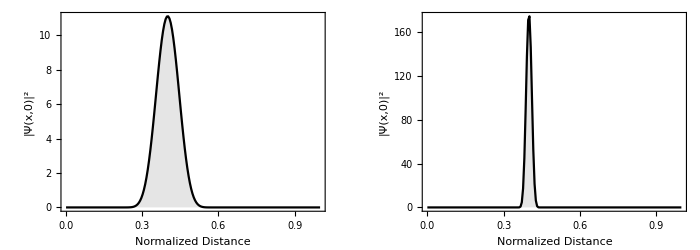

```mathematica
initialstates=GraphicsRow[{
ListPlot[Abs[evol1[[;;,1]]]^2,DataRange->{0,1},PlotRange->{{0,1},{0,All}},PlotStyle->Black,Filling->{1->0},AspectRatio->Full,FillingStyle->Directive[Black,Opacity[0.1]],Frame->True,Joined->True,FrameLabel->{"Normalized Distance","|Ψ(x,0)|^2"}],
ListPlot[Abs[evol2[[;;,1]]]^2,DataRange->{0,1},PlotRange->{{0,1},{0,All}},PlotStyle->Black,Filling->{1->0},AspectRatio->Full,FillingStyle->Directive[Black,Opacity[0.1]],Frame->True,Joined->True,FrameLabel->{"Normalized Distance","|Ψ(x,0)|^2"}]
},ImageSize->{700,250},AspectRatio->Full]
```

```mathematica
Export["initialstates.pdf",initialstates];
```

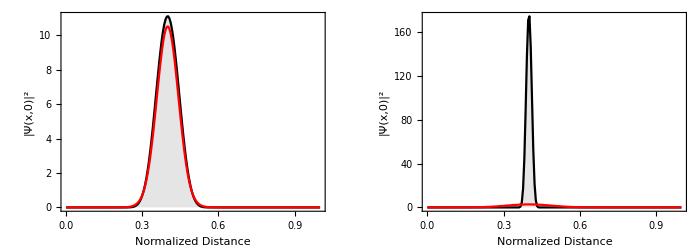

```mathematica
GraphicsRow[{
ListPlot[{Abs[evol1[[;;,1]]]^2,Abs[evol1[[;;,2]]]^2},DataRange->{0,1},PlotRange->{{0,1},{0,All}},PlotStyle->{Black,Red},Filling->{1->0},AspectRatio->Full,FillingStyle->Directive[Black,Opacity[0.1]],Frame->True,Joined->True,FrameLabel->{"Normalized Distance","|Ψ(x,0)|^2"}],
ListPlot[{Abs[evol2[[;;,1]]]^2,Abs[evol2[[;;,2]]]^2},DataRange->{0,1},PlotRange->{{0,1},{0,All}},PlotStyle->{Black,Red},Filling->{1->0},AspectRatio->Full,FillingStyle->Directive[Black,Opacity[0.1]],Frame->True,Joined->True,FrameLabel->{"Normalized Distance","|Ψ(x,0)|^2"}]
},ImageSize->{700,250},AspectRatio->Full]
```

## Visualization

Calculate the trajectory for τ1 < τ < τ2 for a classical particle with dimensionless velocity u and initial position s0 at τ1:

```mathematica
trajectory[s0_,u_,τ1_,τ2_]:=
Module[{dτ,nbounce,bounces},
dτ=Abs[1/u];
nbounce=Ceiling[(τ2-τ1)/dτ];
bounces=If[u>0,
Table[{τ1+((1-s0)+j)dτ,If[OddQ[j],0,1]},{j,0,nbounce}],
Table[{τ1+(s0+j)dτ,If[OddQ[j],1,0]},{j,0,nbounce}]
];
Prepend[bounces,{τ1,s0}]
]
```

```mathematica
Clear[showcoefs]
showcoefs[coefs_,δτ_,nτ_,ns_,OptionsPattern[showcoefs]]:=
With[{
nmodes=Length[coefs],
label=OptionValue["label"],
blank=OptionValue["blank"]
},
Module[{normalized,wgts,evol,cwgt,nshow,dash,lines,epilog},
normalized=coefs/Sqrt[coefs.coefs];
If[blank===True,
ListPlot[{},PlotRangePadding->None,PlotRange->{{0,nτ δτ},{0,1}},FrameLabel->{"Normalized time","Normalized distance"},AspectRatio->Full,Frame->True,Epilog->If[label===None,{},{Text[Style[label,FontSize->Large,FontFamily->"Times",FontSlant->"Italic"],Scaled[{0.5,0.1}],{0,0}]}]],
(* Calculate the evolution of the initial state *)
evol=evolution[normalized,δτ,nτ,ns];
ListDensityPlot[evol,PlotRangePadding->None,DataRange->{{0,nτ δτ},{0,1}},PlotRange->{{0,nτ δτ},{0,1},All},FrameLabel->{"Normalized time","Normalized distance"},ColorFunction->(Blend[{White,Red},Sqrt[#]]&),AspectRatio->Full,Epilog->If[label===None,{},{Text[Style[label,FontSize->Large,FontFamily->"Times",FontSlant->"Italic"],Scaled[{0.5,0.1}],{0,0}]}]
]
]
]
]
Options[showcoefs]={"label"->None,"blank"->False};
```

```mathematica
grid[δτ_,nτ_,ns_,blank_]:=Show[GraphicsGrid[
{
{
showcoefs[{1},δτ,nτ,ns,"label"->"Ψ_1","blank"->blank],
showcoefs[{1,1},δτ,nτ,ns,"label"->"Ψ_1+Ψ_2"],
showcoefs[{1,0,1},δτ,nτ,ns,"label"->"Ψ_1+Ψ_3","blank"->blank]
},
{
showcoefs[{1,-1},δτ,nτ,ns,"label"->"Ψ_1-Ψ_2","blank"->blank],
showcoefs[{0,1},δτ,nτ,ns,"label"->"Ψ_2","blank"->blank],
showcoefs[{0,1,1},δτ,nτ,ns,"label"->"Ψ_2+Ψ_3","blank"->blank]
},
{
showcoefs[{1,0,-1},δτ,nτ,ns,"label"->"Ψ_1-Ψ_3","blank"->blank],
showcoefs[{0,1,-1},δτ,nτ,ns,"label"->"Ψ_2-Ψ_3","blank"->blank],
showcoefs[{0,0,1},δτ,nτ,ns,"label"->"Ψ_3","blank"->blank]
}
},
ImageSize->{1024,768},Spacings->4,AspectRatio->Full
]]
```

```mathematica
blankgrid=Rasterize[Magnify[grid[0.01,200,100,True],2]];
```

```mathematica
Export["superposition_xt_blank.png",blankgrid]
```

superposition_xt_blank.png

```mathematica
supergrid=Rasterize[grid[0.01,200,100]]
```

-Graphics-

```mathematica
Export["superposition_xt.png",supergrid]
```

superposition_xt.png

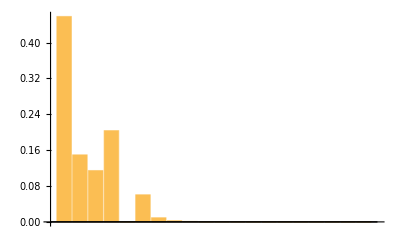

```mathematica
BarChart[Abs[xmode[0.4,0.2,20]]^2,PlotRange->All]
```

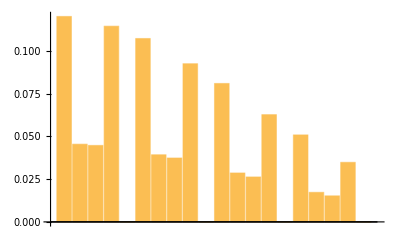

```mathematica
BarChart[Abs[xmode[0.4,0.05,20]]^2,PlotRange->All]
```

```mathematica
Clear[show]
show[s0_,Δs_,δτ_,nτ_,ns_,OptionsPattern[show]]:=
With[{
nmodes=OptionValue["nmodes"],
showlines=OptionValue["showlines"],
magnification=OptionValue["magnification"]
},
Module[{coefs,wgts,evol,cwgt,nshow,dash,lines,epilog},
coefs=xmode[s0,Δs,nmodes];
wgts=Abs[coefs]^2;
(* Calculate the evolution of the initial state *)
evol=evolution[coefs,δτ,nτ,ns];
If[showlines===True,
(* Find how many modes are required to account for 99% of probability *)
cwgt=Accumulate[wgts];
nshow=First[FirstPosition[UnitStep[cwgt-0.99],1]];
(* Prepare lines showing the classical velocities of these modes *)
lines=Table[{Opacity[wgts[[n]]],Line[trajectory[s0,2n,0,nτ δτ]],Line[trajectory[s0,-2n,0,nτ δτ]]},{n,1,nshow}];
epilog={Blue,Thickness[0.01],lines},
epilog={ }
];
Rasterize[Magnify[
ListDensityPlot[evol,PlotRangePadding->None,DataRange->{{0,nτ δτ},{0,1}},PlotRange->{{0,nτ δτ},{0,1},All},FrameLabel->{"Normalized time","Normalized distance"},ColorFunction->(Blend[{White,Red},Sqrt[#]]&),Epilog->epilog],
magnification (* magnification before rasterization *)
]]
]
]
Options[show]={"nmodes"->100,"showlines"->False,"magnification"->1};
```

```mathematica
show[0.4,0.1,0.001,250,200]
```

-Graphics-

```mathematica
show[0.4,0.1,0.005,250,200,showlines->True]
```

-Graphics-

```mathematica
show[0.4,0.1,0.01,250,200]
```

-Graphics-

```mathematica
bigerror=show[0.4,0.2,0.0002,250,200,showlines->True,magnification->2]
```

-Graphics-

```mathematica
show[0.4,0.1,0.0002,250,200,showlines->True]
```

-Graphics-

```mathematica
smallerror=show[0.4,0.05,0.0002,250,200,showlines->True,magnification->2]
```

-Graphics-

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/repo/output/bigerror.png",bigerror];
Export["/Users/david/Documents/uci/Teaching/113A/repo/output/smallerror.png",smallerror];
```